# Hypermatrix Eigenvector Analysis

Numerical Constants

```mathematica
Needs["PlotLegends`"]
SetDirectory[FileNameJoin[{NotebookDirectory[]}]]


L = 5;
m = 20;

MAX=2m+1;

σ = 1;
κ  =1;
Δ = L/(2m)//N;
CreateDirectory[ToString[Δ]]
Print["\nDelta:",Δ,"\n"]

v[η_]:=(σ η^2)/κ

umin = 0;
uMAX=20;


M=Table[0,{i,1,MAX^2},{j,1,MAX^2}];
V[η_, ξ_] :=   v[(2 η)/(√κ)] + v[(η + √3 ξ)/(√κ)] + v[(√3 ξ - η)/(√κ)];
T̂[ η1_, η2_, ξ1_, ξ2_] :=   Exp[-(η1 - η2)^2] Exp[-(ξ1 - ξ2)^2] Exp[-V[η1, ξ1]/2] Exp[-V[η2, ξ2]/2];
OverHat[MT]=Table[ Δ^2 T̂[Δ η1, Δ η2,Δ ξ1, Δ ξ2], {η1, -m,m}, {η2,-m, m}, {ξ1,-m, m}, {ξ2,-m, m}] // N;

r[x_,y_]:=(x-1) MAX+y;
Do[
M[[r[k,i],r[j,l]]]=OverHat[MT][[k,j]][[i,l]],{k,1,MAX},{i,1,MAX},{j,1,MAX},{l,1,MAX}
]
M==Transpose[M];

β=4;
μ=(12 σ)/κ//N;
c=((μ^2+2 β μ)^(1/2))/2//N;
δ=2 c+μ+β;
b=1/2 ((δ^2-β^2)/δ)^(1/2)//N;
k=Log[δ/β]//N;
Subscript[e, 0]=((4 π)/δ)^(1/2)//N;
Subscript[E, 00][h_]:=Subscript[e, 0] Exp[-k h];
Subscript[C, 0]=1/2 ((2 π)/((μ^2+2 β μ)^(1/2)))^(-1/4);
gC[n_]:=(1/(2^n Factorial[n]))^(1/2);

OverHat[λA][n_]:=Subscript[e, 0] Exp[-k n];
OverHat[ψA][n_,η_]:=2 Subscript[C, 0] gC[n] HermiteH[n,b η] Exp[-(c η^2)/2];

OverHat[ψAij][n1_,n2_,η1_,η2_]:=OverHat[ψA][n1,η1]*OverHat[ψA][n2,η2];

FirstEvalλA=0;
LastEvalλA=10;

ψm=(MAX^2-1)/2;

ψ = Δ^-1 Eigenvectors[M];
```

C:\Users\Hemant\Desktop\cor.tar\cor\CORRECTIONSv1\Results\Collagen\Eigensystem\Hypermatrix\Eigenvectors

CreateDirectory::filex: "C:\\Users\\Hemant\\Desktop\\cor.tar\\cor\\CORRECTIONSv1\\Results\\Collagen\\Eigensystem\\Hypermatrix\\Eigenvectors\\0.125\\" already exists.

C:\Users\Hemant\Desktop\cor.tar\cor\CORRECTIONSv1\Results\Collagen\Eigensystem\Hypermatrix\Eigenvectors\0.125

Delta:0.125

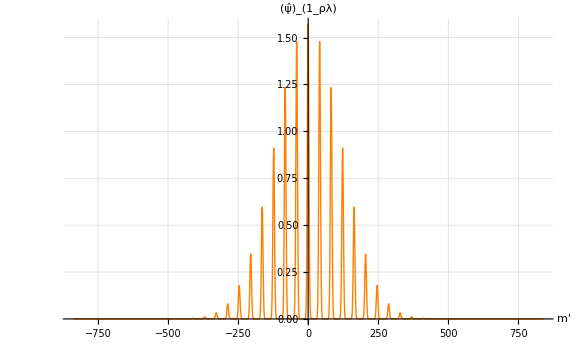
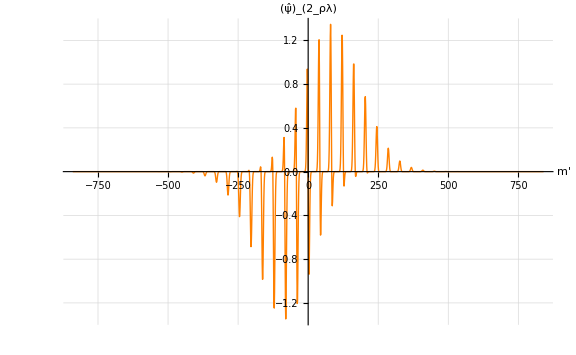
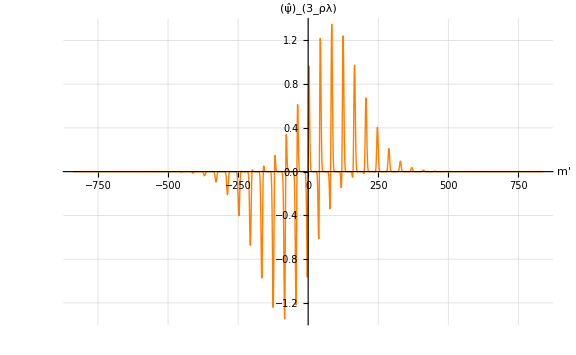
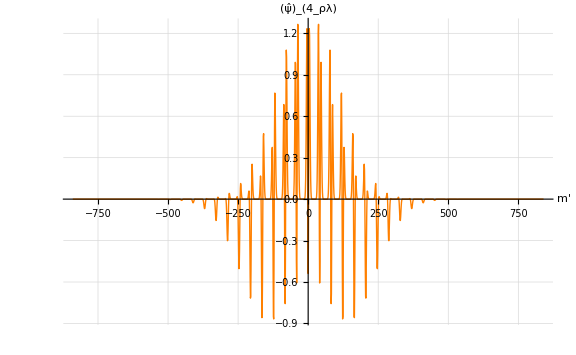

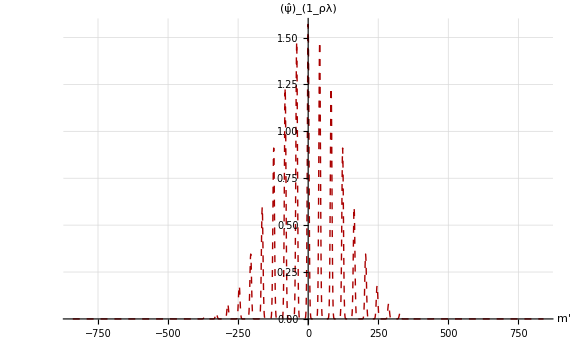
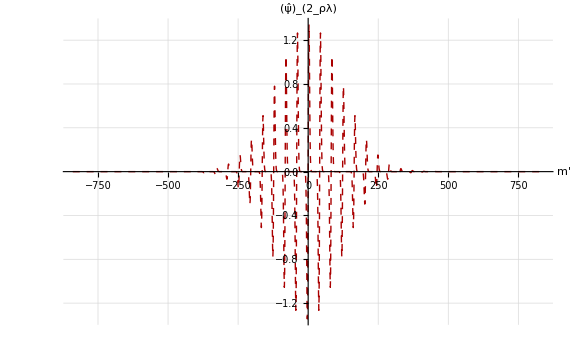
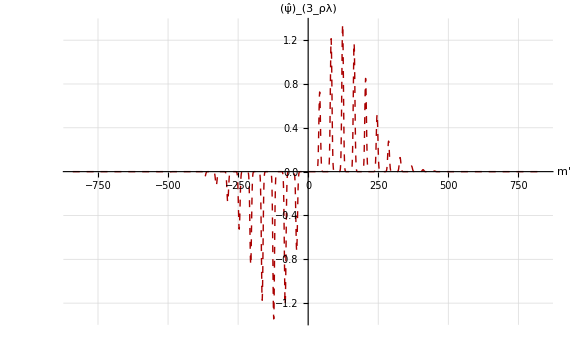
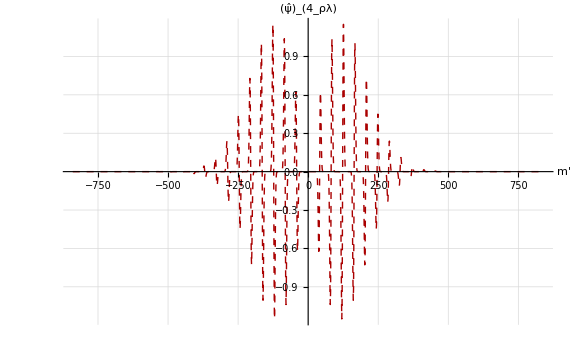

0.125/N_psi_1_L5_m20_k1.pdf

0.125/N_psi_2_L5_m20_k1.pdf

0.125/N_psi_3_L5_m20_k1.pdf

0.125/N_psi_4_L5_m20_k1.pdf

0.125/A_psi_1_L5_m20_k1.pdf

0.125/A_psi_2_L5_m20_k1.pdf

0.125/A_psi_3_L5_m20_k1.pdf

0.125/A_psi_4_L5_m20_k1.pdf

```mathematica
fsAxesLabel=24;
fs2=18;

HypEigen=
Table[
Table[{i,ψ[[x,i+ψm+1]]},{i,-ψm,ψm}],
{x,1,4}
];

HypEigenAnalytical=Table[Flatten[Table[{(i/Δ MAX + j/Δ), 
OverHat[ψAij][x1, x2, i, j]}, {i, -(L/2), 
   L/2, Δ}, {j, -(L/2), L/2, Δ}], 1],{x1,0,2},{x2,0,2}];


HypEigenPlot=Table[
ListLinePlot[
HypEigen[[i]],
ImageSize->Large,
PlotRange->All,
PlotStyle->{Thick,Orange},
AxesLabel->{
Style["m'",FontSize->fsAxesLabel],
Style[Subscript["ψ̂", Subscript[ToString[i], "ρλ"]],FontSize->fsAxesLabel]
},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
LabelStyle->{"Times",FontSize->fs2}
],
{i,1,4}
]

n1=ListLinePlot[HypEigenAnalytical[[1,1]],
ImageSize->Large,
PlotRange->All,
PlotStyle->{Thick,Dashed,Darker[Red]},
AxesLabel->{
Style["m'",FontSize->fsAxesLabel],
Style[Subscript["ψ̂", Subscript[ToString[1], "ρλ"]],FontSize->fsAxesLabel]
},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
LabelStyle->{"Times",FontSize->fs2}
];
n2=ListLinePlot[HypEigenAnalytical[[1,2]],
ImageSize->Large,
PlotRange->All,
PlotStyle->{Thick,Dashed,Darker[Red]},
AxesLabel->{
Style["m'",FontSize->fsAxesLabel],
Style[Subscript["ψ̂", Subscript[ToString[2], "ρλ"]],FontSize->fsAxesLabel]
},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
LabelStyle->{"Times",FontSize->fs2}
];
n3=ListLinePlot[HypEigenAnalytical[[2,1]],
ImageSize->Large,
PlotRange->All,
PlotStyle->{Thick,Dashed,Darker[Red]},
AxesLabel->{
Style["m'",FontSize->fsAxesLabel],
Style[Subscript["ψ̂", Subscript[ToString[3], "ρλ"]],FontSize->fsAxesLabel]
},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
LabelStyle->{"Times",FontSize->fs2}
];
n4=ListLinePlot[HypEigenAnalytical[[2,2]],
ImageSize->Large,
PlotRange->All,
PlotStyle->{Thick,Dashed,Darker[Red]},
AxesLabel->{
Style["m'",FontSize->fsAxesLabel],
Style[Subscript["ψ̂", Subscript[ToString[4], "ρλ"]],FontSize->fsAxesLabel]
},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
LabelStyle->{"Times",FontSize->fs2}
];
{n1,n2,n3,n4}


Export[ToString[Δ]<>"/N_psi_1_L"<>ToString[L]<>"_m"<>ToString[m]<>"_k"<>ToString[κ]<>".pdf",HypEigenPlot[[1]]]
Export[ToString[Δ]<>"/N_psi_2_L"<>ToString[L]<>"_m"<>ToString[m]<>"_k"<>ToString[κ]<>".pdf",HypEigenPlot[[2]]]
Export[ToString[Δ]<>"/N_psi_3_L"<>ToString[L]<>"_m"<>ToString[m]<>"_k"<>ToString[κ]<>".pdf",HypEigenPlot[[3]]]
Export[ToString[Δ]<>"/N_psi_4_L"<>ToString[L]<>"_m"<>ToString[m]<>"_k"<>ToString[κ]<>".pdf",HypEigenPlot[[4]]]

Export[ToString[Δ]<>"/A_psi_1_L"<>ToString[L]<>"_m"<>ToString[m]<>"_k"<>ToString[κ]<>".pdf",n1]
Export[ToString[Δ]<>"/A_psi_2_L"<>ToString[L]<>"_m"<>ToString[m]<>"_k"<>ToString[κ]<>".pdf",n2]
Export[ToString[Δ]<>"/A_psi_3_L"<>ToString[L]<>"_m"<>ToString[m]<>"_k"<>ToString[κ]<>".pdf",n3]
Export[ToString[Δ]<>"/A_psi_4_L"<>ToString[L]<>"_m"<>ToString[m]<>"_k"<>ToString[κ]<>".pdf",n4]
```

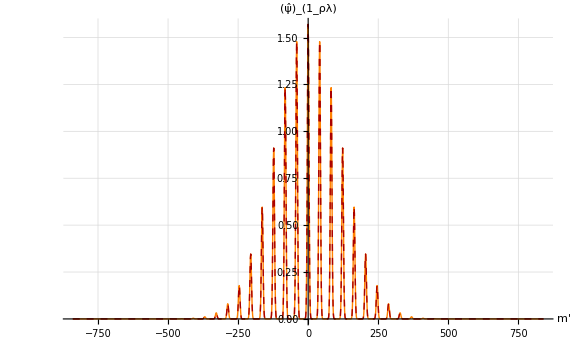

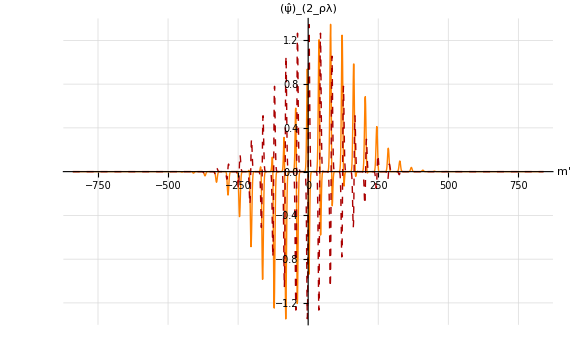

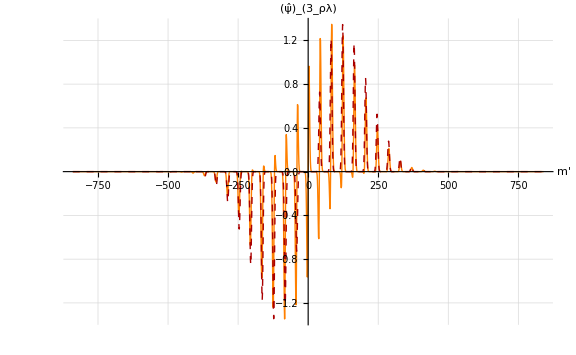

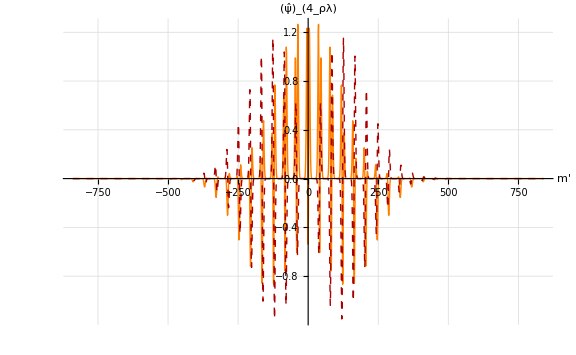

0.125/NA_psi_1_L5_m20_k1.pdf

0.125/NA_psi_2_L5_m20_k1.pdf

0.125/NA_psi_3_L5_m20_k1.pdf

0.125/NA_psi_4_L5_m20_k1.pdf

```mathematica
legend={{Graphics[{Thick,Dashed,Darker[Red],Line[{{0,0},{2,0}}]}],Style["Numerical",FontSize->fs2]},{Graphics[{Thick,Orange,Line[{{0,0},{2,0}}]}],Style["Analytical",FontSize->fs2]}};

s1=ShowLegend[Show[{HypEigenPlot[[1]],n1}],{legend,LegendShadow->None,LegendBorder->None,LegendBackground->Opacity[0],ShadowBackground->Opacity[0],LegendSize->0.5,LegendPosition->{0.3,0.2}}
]

s2=ShowLegend[Show[{HypEigenPlot[[2]],n2}],{legend,LegendShadow->None,LegendBorder->None,LegendBackground->Opacity[0],ShadowBackground->Opacity[0],LegendSize->0.5,LegendPosition->{0.3,0.2}}
]

s3=ShowLegend[Show[{HypEigenPlot[[3]],n3}],{legend,LegendShadow->None,LegendBorder->None,LegendBackground->Opacity[0],ShadowBackground->Opacity[0],LegendSize->0.5,LegendPosition->{0.3,0.2}}
]

s4=ShowLegend[Show[{HypEigenPlot[[4]],n4}],{legend,LegendShadow->None,LegendBorder->None,LegendBackground->Opacity[0],ShadowBackground->Opacity[0],LegendSize->0.5,LegendPosition->{0.3,0.2}}
]

Export[ToString[Δ]<>"/NA_psi_1_L"<>ToString[L]<>"_m"<>ToString[m]<>"_k"<>ToString[κ]<>".pdf",s1]
Export[ToString[Δ]<>"/NA_psi_2_L"<>ToString[L]<>"_m"<>ToString[m]<>"_k"<>ToString[κ]<>".pdf",s2]
Export[ToString[Δ]<>"/NA_psi_3_L"<>ToString[L]<>"_m"<>ToString[m]<>"_k"<>ToString[κ]<>".pdf",s3]
Export[ToString[Δ]<>"/NA_psi_4_L"<>ToString[L]<>"_m"<>ToString[m]<>"_k"<>ToString[κ]<>".pdf",s4]
```

```mathematica
NLPA=Table[
ListPlot3D[Flatten[Table[{Δ i,Δ j,Partition[Table[HypEigen[[x]][[i+ψm+1,2]],{i,-ψm,ψm,1}],MAX][[i+m+1,j+m+1]]},{i,-m,m},{j,-m,m}],1],
ImageSize->Large,
AxesLabel->{
Style["ρ",FontSize->fsAxesLabel],
Style["λ",FontSize->fsAxesLabel],
Style[Subscript["ψ̂", Subscript[ToString[x], "ρλ"]],FontSize->fsAxesLabel]
},
PlotRange->All,
Ticks->{{-2,0,2},{-2,0,2},{1,0,-1}},
LabelStyle->{"Times",FontSize->fs2}
],
{x,1,3}];
```

```mathematica
{NLPA[[1]],NLPA[[2]],NLPA[[3]]}
Export[ToString[Δ]<>"/3D_N_psi_1_L"<>ToString[L]<>"_m"<>ToString[m]<>"_k"<>ToString[κ]<>".pdf",Rasterize[NLPA[[1]],ImageResolution->200]]
Export[ToString[Δ]<>"/3D_N_psi_2_L"<>ToString[L]<>"_m"<>ToString[m]<>"_k"<>ToString[κ]<>".pdf",Rasterize[NLPA[[2]],ImageResolution->200]]
Export[ToString[Δ]<>"/3D_N_psi_3_L"<>ToString[L]<>"_m"<>ToString[m]<>"_k"<>ToString[κ]<>".pdf",Rasterize[NLPA[[3]],ImageResolution->200]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

0.125/3D_N_psi_1_L5_m20_k1.pdf

0.125/3D_N_psi_2_L5_m20_k1.pdf

0.125/3D_N_psi_3_L5_m20_k1.pdf

```mathematica
data3DψA00 = Flatten[Table[{i, j, OverHat[ψAij][0, 0, i, j]}, {i, -(L/2),      L/2, Δ}, {j, -(L/2), L/2, Δ}], 1];
data3DψA10 = Flatten[Table[{i, j, OverHat[ψAij][1, 0, i, j]}, {i, -(L/2),      L/2, Δ}, {j, -(L/2), L/2, Δ}], 1];
data3DψA01 = Flatten[Table[{i, j, OverHat[ψAij][0, 1, i, j]}, {i, -(L/2),      L/2, Δ}, {j, -(L/2), L/2, Δ}], 1];

LPA00 = ListPlot3D[data3DψA00, 
ImageSize->Large,AxesLabel->{
Style["ρ",FontSize->fsAxesLabel],
Style["λ",FontSize->fsAxesLabel],
Style[Subscript["ψ̂", Subscript[ToString[1], "ρλ"]],FontSize->fsAxesLabel]
},
PlotRange->All,
Ticks->{{-2,0,2},{-2,0,2},{1,0,-1}},
LabelStyle->{"Times",FontSize->fs2}
];
LPA10 = ListPlot3D[data3DψA10, 
ImageSize->Large,AxesLabel->{
Style["ρ",FontSize->fsAxesLabel],
Style["λ",FontSize->fsAxesLabel],
Style[Subscript["ψ̂", Subscript[ToString[2], "ρλ"]],FontSize->fsAxesLabel]
},
PlotRange->All,
Ticks->{{-2,0,2},{-2,0,2},{1,0,-1}},
LabelStyle->{"Times",FontSize->fs2}
];
LPA01 = ListPlot3D[data3DψA01, 
ImageSize->Large,AxesLabel->{
Style["ρ",FontSize->fsAxesLabel],
Style["λ",FontSize->fsAxesLabel],
Style[Subscript["ψ̂", Subscript[ToString[3], "ρλ"]],FontSize->fsAxesLabel]
},
PlotRange->All,
Ticks->{{-2,0,2},{-2,0,2},{1,0,-1}},
LabelStyle->{"Times",FontSize->fs2}
];

{LPA00,LPA01,LPA10}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
α =(π/4);
trans[ι_, φ_] := Flatten[RotationMatrix[α].({
     {ι},
     {φ}
    }), 1]

Rdata3DψA00 = Flatten[Table[{i, j, OverHat[ψAij][0, 0, trans[i, j][[1]],       trans[i, j][[2]]]}, {i, -(L/2), L/2, Δ}, {j, -(L/2), L/2, Δ}], 1];
Rdata3DψA10 = Flatten[Table[{i, j, OverHat[ψAij][1, 0, trans[i, j][[1]],       trans[i, j][[2]]]}, {i, -(L/2), L/2, Δ}, {j, -(L/2), L/2, Δ}], 1];
Rdata3DψA01 = Flatten[Table[{i, j, OverHat[ψAij][0, 1, trans[i, j][[1]],       trans[i, j][[2]]]}, {i, -(L/2), L/     2, Δ}, {j, -(L/2), L/2, Δ}], 1];

RLPA00 = ListPlot3D[Rdata3DψA00,
ImageSize->Large,
AxesLabel->{
Style["ρ",FontSize->fsAxesLabel],
Style["λ",FontSize->fsAxesLabel],
Style[Subscript["ψ̂", Subscript[ToString[1], "ρλ"]],FontSize->fsAxesLabel]
},
PlotRange->All,
Ticks->{{-2,0,2},{-2,0,2},{1,0,-1}},
LabelStyle->{"Times",FontSize->fs2}
];

RLPA10 = ListPlot3D[Rdata3DψA10,
ImageSize->Large,
AxesLabel->{
Style["ρ",FontSize->fsAxesLabel],
Style["λ",FontSize->fsAxesLabel],
Style[Subscript["ψ̂", Subscript[ToString[2], "ρλ"]],FontSize->fsAxesLabel]
},
PlotRange->All,
Ticks->{{-2,0,2},{-2,0,2},{1,0,-1}},
LabelStyle->{"Times",FontSize->fs2}
];

RLPA01 = ListPlot3D[Rdata3DψA01, 
ImageSize->Large,
AxesLabel->{
Style["ρ",FontSize->fsAxesLabel],
Style["λ",FontSize->fsAxesLabel],
Style[Subscript["ψ̂", Subscript[ToString[3], "ρλ"]],FontSize->fsAxesLabel]
},
PlotRange->All,
Ticks->{{-2,0,2},{-2,0,2},{1,0,-1}},
LabelStyle->{"Times",FontSize->fs2}
];

{RLPA00 ,RLPA01 ,RLPA10 }

Export[ToString[Δ]<>"/3D_A_psi_00_L"<>ToString[L]<>"_m"<>ToString[m]<>"_k"<>ToString[κ]<>".pdf",Rasterize[RLPA00,ImageResolution->200]]
Export[ToString[Δ]<>"/3D_A_psi_01_L"<>ToString[L]<>"_m"<>ToString[m]<>"_k"<>ToString[κ]<>".pdf",Rasterize[RLPA01,ImageResolution->200]]
Export[ToString[Δ]<>"/3D_A_psi_10_L"<>ToString[L]<>"_m"<>ToString[m]<>"_k"<>ToString[κ]<>".pdf",Rasterize[RLPA10,ImageResolution->200]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

0.125/3D_A_psi_00_L5_m20_k1.pdf

0.125/3D_A_psi_01_L5_m20_k1.pdf

0.125/3D_A_psi_10_L5_m20_k1.pdf

2D Eigenmatrix Comparisons

```mathematica
{NLPA[[1]],RLPA00}
```

{-Graphics3D-,-Graphics3D-}

```mathematica
{NLPA[[3]],RLPA01}
{NLPA[[2]],RLPA10}
```

{-Graphics3D-,-Graphics3D-}

{-Graphics3D-,-Graphics3D-}